```mathematica
(*This file splices the v(T) relation coming from BSMPT
and putputs new files. This code is adapted for CP in the Dark.*)
```

## Make Table

```mathematica
filename="inBSMPT";
```

#### Run Terminal Commands

```mathematica
SetDirectory[NotebookDirectory[]];
```

<|ExitCode→0,StandardOutput→,StandardError→|>

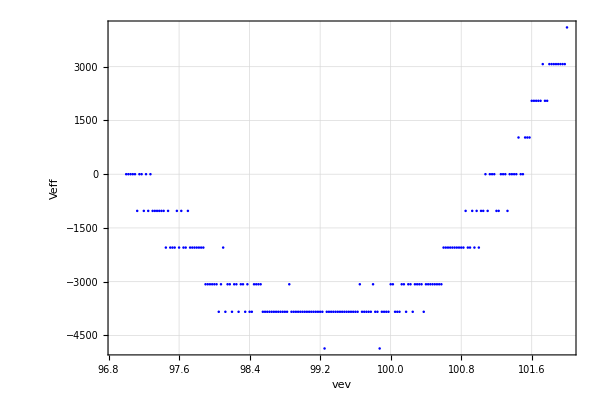

```mathematica
RunProcess[{"./build/macos-armv8-release/bin/PotPlotter",
"--model=cpinthedark",
"--input="<>filename<>".tsv",
"--output="<>filename<>"_out.tsv",
"--line=3",
"--temperature=165.989",
"--slice=true",
"--npoints=200",
"--min_start=97",
"--min_end=102"}]
raw=Import[filename<>"_out.tsv","Table"]/."nan"->0;
headers=First[raw];
rows=Rest[raw]//Chop[#,10^-4]&;
data=Dataset[AssociationThread[headers,#]&/@rows];
vev=data[[All,"omega_1"]]//SetPrecision[#,100]&//Normal;
Veff=data[[All,"Veff(v,T)"]]//SetPrecision[#,100]&//Normal;
ListPlot[{Transpose[{vev,Veff-Veff[[1]]}]},
PlotRange->All,
PlotTheme->"Detailed",
Frame->True,FrameStyle->Directive[{Black,Thick}],
FrameLabel->{Style["vev",Italic,Black,FontFamily->"Latin Modern Roman",FontSize->16],
Style["Veff",Italic,Black,FontFamily->"Latin Modern Roman",FontSize->16]},
LabelStyle->{FontFamily->"Latin Modern Roman",16,GrayLevel[0]},
AspectRatio->0.7,
PlotStyle->{{Blue, PointSize[0.003]},{Red, PointSize[0.01]}},
ImageSize->600,
Joined->False,
GridLinesStyle->Directive[Gray,Dashed, Thickness[0.001]]]
```

#### Temperatures and VEVs